## Nonresonant scattering

Constants

```mathematica
ℏ = 1.054571596 10^-27;c=2.99792458 10^10;Subscript[m, e]=9.10938188 10^-28; Subscript[α, e]=7.297352533 10^-3;
```

```mathematica
Subscript[Gm, e]= 1.16639 10^-5( 0.510998902 10^-3)^2
```

3.04568×10^-12

```mathematica
Subscript[g, Ve]=1/2+2 (0.23);Subscript[g, Vμ]=-1/2+2( 0.23);Subscript[g, Ae]=1/2;Subscript[g, Aμ]=-1/2;Subscript[g, V]=√(Subscript[g, Ve]^2+2 Subscript[g, Vμ]^2);Subscript[g, A]=√(Subscript[g, Ae]^2+2 Subscript[g, Aμ]^2);
```

```mathematica
Subscript[g, V]^2/Subscript[g, A]^2-1
```

0.233067

```mathematica
Subscript[λ, e]= ℏ/(Subscript[m, e] c)
Subscript[τ, e] =Subscript[λ, e]/c
Subscript[E, e] = Subscript[m, e] c^2
Subscript[Q, e] = Subscript[E, e]/(Subscript[λ, e]^3 Subscript[τ, e]) 
 Subscript[N, e] = 1/(Subscript[λ, e]^3 Subscript[τ, e])
```

3.86159×10^-11

1.28809×10^-21

8.1871×10^-7

1.10379×10^46

1.3482×10^52

```mathematica
Integrate[x √(x^2-1) Exp[-x*y],{x,1,∞},Assumptions->{y>0}]
```

(K_2(y))/y

```mathematica
Integrate[x √((x^2-1)^3) Exp[-x*y],{x,1,∞},Assumptions->{y>0}]
```

(3 K_3(y))/y^2

```mathematica
Series[BesselK[3,y],{y,∞,1}]
```

ⅇ^-y (√(π/2) √(1/y)+O((1/y)^(3/2)))

```mathematica
96*3
```

288

```mathematica
F11[y_]:=NIntegrate[(y^9 x^2)/(Exp[y*√(x^2+1)]-1),{x,0,∞}];
```

```mathematica
F11[0.01]
```

2.40382×10^-12

```mathematica
Series[x^7 ArcSin[1/x]-x/15 (x^2-1)^(1/2) (8+10 x^2+15 x^4),{x,∞,2}]
```

16/35+8/45 (1/x)^2+O((1/x)^3)

```mathematica
Integrate[(1-x^2)^3 (1-x^2 a^2),{x,0,1}]
```

16/35-(16 a^2)/315

```mathematica
Integrate[((1-z^2)^3)/((1-z^2/x^2)^(7/2)),{z,0,1},Assumptions->{x>1}]
```

x^7 csc^-1(x)-1/15 x √(x^2-1) (15 x^4+10 x^2+8)

```mathematica
Integrate[z^4/(Exp[z]-1),{z,0,∞}]
```

24 ζ(5)

```mathematica
F1[y_]:=1/96 NIntegrate[(x(Subscript[g, V]^2+Subscript[g, A]^2 (x^2-1))√(x^2-1))/(Exp[x y]-1) (x^7 ArcSin[1/x]-x/15 (x^2-1)^(1/2) (8+10 x^2+15 x^4)),{x,1,∞},PrecisionGoal->4];
```

```mathematica
F1[0.05]
```

284587.

```mathematica
F2[y_]:=1/210 NIntegrate[((x^2-1/9) (Subscript[g, V]^2+Subscript[g, A]^2 (x^2-1)))/(Exp[x y]-1),{x,1,∞},PrecisionGoal->4];
```

```mathematica
F2[0.05]
```

284423.

```mathematica
G1[y_]:=1/96 NIntegrate[(x(Subscript[g, V]^2+2/3 Subscript[g, A]^2 (x^2-1))x √(x^2-1))/(Exp[x y]-1) ,{x,1,∞}];
```

```mathematica
G1[1]
```

0.643682

```mathematica
G2[y_]:=1/128 NIntegrate[(x √(x^2-1) (x^2+0.24))/(Exp[x y]-1),{x,1,∞}];
```

```mathematica
G2[1]
```

0.187826

** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ***

```mathematica
R[a_]:=(12 √a)/(√π) Exp[2 a] NIntegrate[Exp[-a v] (v+1/a) *(t^3 (v^2 t -(1-t)^-1))/((1-t)^3(1-Exp[-a (v t - (v-v t)^-1)])),{v,0,∞},{t,0,1},Method  -> QuasiMonteCarlo, MaxPoints-> 1000000,Compiled->False,PrecisionGoal->4];
```

```mathematica
R[0.1]
```

2.39816×10^16

```mathematica
R11[a_]:=(12 √a)/(√π) Exp[2 a] NIntegrate[Exp[-a v] (v+1/a) *(t^3 (v^2 t -(1-t)^-1))/((1-t)^3(1-Exp[-a (v t - (v-v t)^-1)])),{v,0,∞},{t,0,1,1},PrecisionGoal->4];
```

```mathematica
R11[0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3.7506×10^11

```mathematica
R12[a_]:=(3 a^(3/2))/(√π) Exp[2 a] NIntegrate[Exp[-a v] v^2 *(t^4 (v^2 t -(1-t)^-1) (v^2 -(1-t)^-2)(-(1-t)^-1+(v^2 t)/5))/((1-Exp[-a (v t - (v-v t)^-1)]) (1-Exp[-a (v (1-t) + (v-v t)^-1)])),{v,0,∞},{t,0,1,1},PrecisionGoal->5];
```

```mathematica
R12[1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

56249.4

```mathematica
ff1[a_,t_,v_]:=(3 a^(3/2))/(√π) Exp[2 a] *Exp[-a v] v^2 *(t^4 (v^2 t -(1-t)^-1) (v^2 -(1-t)^-2)(-(1-t)^-1+(v^2 t)/5))/((1-Exp[-a (v t - (v-v t)^-1)]) (1-Exp[-a (v (1-t) + (v-v t)^-1)]));
```

```mathematica
Plot[ff1[12,t,20],{t,0.95,0.999}]
```

```mathematica
RR00[0.01]/R12[0.01]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.00304

```mathematica
R12[135]/RR00[135]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.991679

```mathematica
FullSimplify[15/(8 π^8)Integrate[x^5 (x^2-y^2/5)Exp[-x],{x,y,∞},Assumptions->y>0]]
```

(3 ⅇ^-y (y (y (y (y (y (y (2 y+15)+95)+495)+2040)+6240)+12600)+12600))/(4 π^8)

```mathematica
F2[y_]:=15/(8 π^8)NIntegrate[(x^5 (x^2-y^2/5))/(Exp[x]-1),{x,y,∞}];
```

```mathematica
F2[0.1]
```

0.999952

```mathematica
F0[y_]:=(3 ⅇ^-y y^7)/(2 π^8)+(45 ⅇ^-y y^6)/(4 π^8)+(285 ⅇ^-y y^5)/(4 π^8)+(1485 ⅇ^-y y^4)/(4 π^8)+(1530 ⅇ^-y y^3)/π^8+(4680 ⅇ^-y y^2)/π^8+(9450 ⅇ^-y y)/π^8+(9450 ⅇ^-y)/π^8;
```

```mathematica
F0[0]//N
```

0.995939

```mathematica
Plot[F0[x]/F2[x],{x,0,20},Frame->True]
```

```mathematica
ff1=Plot[{F2[x],1,F0[x]},{x,0,20},Frame->True,RotateLabel->False,FrameLabel->{"qp","ql"},PlotRange->{{0,20},{0,1.2}},PlotStyle->{Black,Dashing[{0.001,0.01}],Dashing[{0.01,0.01}]}]
```

NIntegrate::nlim: TraditionalForm`x = TraditionalForm`x is not a valid limit of integration.

General::stop: Further output of TraditionalForm`NIntegrate :: "nlim" will be suppressed during this calculation.

```mathematica
Export["fig11.eps",ff1,"eps"];
```

```mathematica
Qs=(8 π^2 Subscript[Gm, e]^2 Subscript[α, e])/4725(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (22.68)^2 (0.017)^9
```

1.27554×10^6

```mathematica
NIntegrate[Exp[-z] (z+1) *z^3 (2 PolyLog[3,Exp[z]]-z PolyLog[2,Exp[z]]),{z,0,∞},PrecisionGoal->4]
```

1438.74+2.51319506015487×10^-865 ⅈ

```mathematica
Integrate[Exp[-z] (z+1) *z^3 (2 PolyLog[3,Exp[z]]-z PolyLog[2,Exp[z]]),{z,0,∞}]
```

48 π^2+(14 π^4)/5+(8 π^6)/63+72 (4 ζ(3)+3 ζ(5))

```mathematica
Rsmall[a_]:=(12 Exp[2 a] 1439)/(√π a^(15/2));
```

```mathematica
Rsmall[0.5]
```

4.79387×10^6

```mathematica
vF=.
```

```mathematica
QQ1=(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] 22.68((2 Subscript[α, e] 22.68)/π vF)^(15/4) (((0.34*1000)/22.68)^2+1)^-3(0.02)^(3/2) Exp[-((2 Subscript[α, e] 22.68)/(π (0.02)^2)vF)^(1/2)] R11[1/2((2 Subscript[α, e] 22.68)/(π (0.02)^2) vF)^(1/2)]
```

0.0000771896

```mathematica
QQ10=(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (1000/4.41)((2 Subscript[α, e](1000/4.41))/π )^(15/4) (((0.34*1000)/(1000/4.41))^2+1)^-3(0.17)^(3/2) Exp[-((2 Subscript[α, e] (1000/4.41))/(π (0.17)^2))^(1/2)]
```

1.19128×10^11

```mathematica
(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] 0.227 ((2 Subscript[α, e] 0.227)/π vF)^(15/4) (((2*28*1)/(3*56*0.227))^2*1.009^6)^-3(0.02)^(3/2) Exp[-((2 Subscript[α, e] 0.227)/(π (0.02)^2) vF)^(1/2)]R11[1/2((2 Subscript[α, e] 0.227)/(π (0.02)^2) vF)^(1/2)]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1291.02

```mathematica
(2 28)/(3 56)//N
```

0.333333

```mathematica
(2 Subscript[α, e])/π(((0.34*1000)/(100/4.41))^2+1)^(1/2)
```

0.0698115

```mathematica
(((0.34*1000)/(100/4.41))^2+1)^(1/2)
```

15.0273

```mathematica
(1000/4.41)
```

226.757

```mathematica
0.5((2 Subscript[α, e] (1000/4.41))/(π (0.17)^2))^(1/2)
```

3.01873

```mathematica
vF=√(1-μ1^-2)
```

0.997783

```mathematica
μ1=√(((0.34*1000)/22.68)^2+1)
```

15.0245

```mathematica
√((2 Subscript[α, e]  22.68)/(π (0.017)^2) vF)
```

19.0727

```mathematica
WW1={};a=.;
For[a=0, a≤ 100,WW1=Append[WW1,{a,R12[a]}],a=a+0.5];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

```mathematica
StandardForm[WW1]
```

{{0.5,4.57513×10^6},{1.,56249.4},{1.5,5528.66},{2.,1236.15},{2.5,426.361},{3.,191.409},{3.5,102.351},{4.,61.8834},{4.5,40.9442},{5.,29.003},{5.5,21.6761},{6.,16.8724},{6.5,13.5936},{7.,11.259},{7.5,9.54103},{8.,8.2411},{8.5,7.23388},{9.,6.43758},{9.5,5.7967},{10.,5.27287},{10.5,4.83885},{11.,4.47483},{11.5,4.16623},{12.,3.90205},{12.5,3.67401},{13.,3.47557},{13.5,3.30075},{14.,3.14769},{14.5,3.01175},{15.,2.8904},{15.5,2.78155},{16.,2.68348},{16.5,2.59474},{17.,2.51412},{17.5,2.44062},{18.,2.37338},{18.5,2.31167},{19.,2.25487},{19.5,2.20244},{20.,2.15394},{20.5,2.10894},{21.,2.06712},{21.5,2.02806},{22.,1.99162},{22.5,1.95748},{23.,1.92549},{23.5,1.89548},{24.,1.86723},{24.5,1.84062},{25.,1.8155},{25.5,1.79177},{26.,1.7693},{26.5,1.74816},{27.,1.72782},{27.5,1.70863},{28.,1.69039},{28.5,1.67301},{29.,1.65645},{29.5,1.64065},{30.,1.62556},{30.5,1.61114},{31.,1.59733},{31.5,1.58441},{32.,1.57146},{32.5,1.55931},{33.,1.54764},{33.5,1.53644},{34.,1.52567},{34.5,1.51468},{35.,1.50472},{35.5,1.49512},{36.,1.48587},{36.5,1.47695},{37.,1.46834},{37.5,1.46002},{38.,1.45198},{38.5,1.44423},{39.,1.43672},{39.5,1.42945},{40.,1.42241},{40.5,1.41558},{41.,1.40898},{41.5,1.40257},{42.,1.39636},{42.5,1.39033},{43.,1.38448},{43.5,1.3788},{44.,1.37327},{44.5,1.3679},{45.,1.36268},{45.5,1.35761},{46.,1.35267},{46.5,1.34785},{47.,1.34317},{47.5,1.33861},{48.,1.33417},{48.5,1.32984},{49.,1.32562},{49.5,1.3215},{50.,1.31748},{50.5,1.31357},{51.,1.30973},{51.5,1.306},{52.,1.30235},{52.5,1.29878},{53.,1.2953},{53.5,1.2919},{54.,1.28857},{54.5,1.28531},{55.,1.28213},{55.5,1.27902},{56.,1.27597},{56.5,1.27299},{57.,1.27007},{57.5,1.26721},{58.,1.26441},{58.5,1.26166},{59.,1.25898},{59.5,1.25634},{60.,1.25376},{60.5,1.25123},{61.,1.24875},{61.5,1.24631},{62.,1.24393},{62.5,1.24158},{63.,1.23928},{63.5,1.23703},{64.,1.23482},{64.5,1.23264},{65.,1.23051},{65.5,1.22841},{66.,1.22635},{66.5,1.22433},{67.,1.22234},{67.5,1.22039},{68.,1.21847},{68.5,1.21658},{69.,1.21473},{69.5,1.21291},{70.,1.21111},{70.5,1.20935},{71.,1.20762},{71.5,1.20591},{72.,1.20423},{72.5,1.20258},{73.,1.20095},{73.5,1.19935},{74.,1.19777},{74.5,1.19622},{75.,1.1947},{75.5,1.19319},{76.,1.19171},{76.5,1.19025},{77.,1.18882},{77.5,1.1874},{78.,1.18601},{78.5,1.18463},{79.,1.18328},{79.5,1.18194},{80.,1.18063},{80.5,1.17933},{81.,1.17805},{81.5,1.17679},{82.,1.17555},{82.5,1.17432},{83.,1.17311},{83.5,1.17204},{84.,1.17086},{84.5,1.1697},{85.,1.16855},{85.5,1.16742},{86.,1.16629},{86.5,1.16521},{87.,1.16412},{87.5,1.16305},{88.,1.16142},{88.5,1.16084},{89.,1.1598},{89.5,1.15879},{90.,1.15778},{90.5,1.15679},{91.,1.15581},{91.5,1.15484},{92.,1.15388},{92.5,1.15294},{93.,1.152},{93.5,1.15108},{94.,1.15017},{94.5,1.14927},{95.,1.14787},{95.5,1.14701},{96.,1.14616},{96.5,1.14532},{97.,1.14449},{97.5,1.14367},{98.,1.14285},{98.5,1.14205},{99.,1.14125},{99.5,1.14046},{100.,1.13968},{100.5,1.13891}}

```mathematica
WW1={{0.5,4.575134606233091*^6},{1.,56249.42359897693},{1.5,5528.656405796583},{2.,1236.1548458491752},{2.5,426.36054764071224},{3.,191.40910502958945},{3.5,102.35113746411179},{4.,61.88340599891634},{4.5,40.94418677964016},{5.,29.002979097177956},{5.5,21.676087468787557},{6.,16.872360843801005},{6.5,13.593621932467382},{7.,11.259023353935888},{7.5,9.541025158574726},{8.,8.241102638665206},{8.5,7.233884634923544},{9.,6.437580148084291},{9.5,5.7967039804349065},{10.,5.272873941644391},{10.5,4.838849909014236},{11.,4.47483337944216},{11.5,4.166234934478586},{12.,3.902050103810411},{12.5,3.674009227382607},{13.,3.47556882085945},{13.5,3.300748999096806},{14.,3.1476862040064972},{14.5,3.011749722404802},{15.,2.8904013999904348},{15.5,2.7815535811281147},{16.,2.683476494396234},{16.5,2.5947387388598258},{17.,2.5141221579356343},{17.5,2.440615417324892},{18.,2.3733829182927093},{18.5,2.311673171487575},{19.,2.2548738559777406},{19.5,2.20244413923348},{20.,2.153935250788873},{20.5,2.1089389165127224},{21.,2.0671231224415303},{21.5,2.028058545723905},{22.,1.991624085649922},{22.5,1.9574849991369137},{23.,1.9254949028465562},{23.5,1.8954759665816023},{24.,1.8672331083043934},{24.5,1.8406154169366586},{25.,1.8155047155314006},{25.5,1.7917696693915508},{26.,1.7693045653692132},{26.5,1.748157898958331},{27.,1.727821607464554},{27.5,1.7086343568707},{28.,1.6903864683762504},{28.5,1.6730124209672788},{29.,1.6564526383958778},{29.5,1.640652789397836},{30.,1.6255635764436658},{30.5,1.6111402227094407},{31.,1.59732966312517},{31.5,1.584409799280563},{32.,1.5714575598108467},{32.5,1.5593072855063157},{33.,1.5476438727175066},{33.5,1.5364390928055764},{34.,1.5256670950958322},{34.5,1.5146754340447093},{35.,1.5047168337916597},{35.5,1.495118217059977},{36.,1.4858668402180393},{36.5,1.4769464541188353},{37.,1.468337189597445},{37.5,1.4600231879345689},{38.,1.4519786741477057},{38.5,1.4442253321930254},{39.,1.4367248416244103},{39.5,1.429454468505521},{40.,1.4224086177431907},{40.5,1.4155847200604386},{41.,1.4089789808223367},{41.5,1.4025742487289303},{42.,1.3963616356928679},{42.5,1.3903328452321826},{43.,1.3844799517937125},{43.5,1.3787954136641254},{44.,1.3732721952476254},{44.5,1.36789974414976},{45.,1.3626804349937305},{45.5,1.3576069202102443},{46.,1.3526665460275114},{46.5,1.3478535014720587},{47.,1.3431712465866856},{47.5,1.338611043311828},{48.,1.334167384090567},{48.5,1.3298402311569046},{49.,1.3256174504584817},{49.5,1.3214994036986318},{50.,1.3174815919110563},{50.5,1.313573723931118},{51.,1.3097344892924536},{51.5,1.3059981404211756},{52.,1.3023491775767255},{52.5,1.2987844579558983},{53.,1.2953014883291005},{53.5,1.291897411137487},{54.,1.2885695279529263},{54.5,1.285314881468247},{55.,1.2821310177813012},{55.5,1.279016585403634},{56.,1.2759701984905207},{56.5,1.2729873434231862},{57.,1.2700673119065478},{57.5,1.2672080457242403},{58.,1.26440779302794},{58.5,1.2616648085006141},{59.,1.258977056965993},{59.5,1.2563429032244018},{60.,1.2537612736597497},{60.5,1.2512288533324725},{61.,1.2487471099664278},{61.5,1.2463131288134723},{62.,1.2439252659153865},{62.5,1.2415829730337988},{63.,1.239284989534984},{63.5,1.237030474523309},{64.,1.234815970937534},{64.5,1.2326421857583654},{65.,1.2305080072217807},{65.5,1.2284117632190796},{66.,1.2263526064201042},{66.5,1.22432992150798},{67.,1.2223412387042352},{67.5,1.2203897550695435},{68.,1.218470452736129},{68.5,1.216583976362351},{69.,1.2147305764617122},{69.5,1.212906947840206},{70.,1.2111137383411206},{70.5,1.209350162729735},{71.,1.207615338908412},{71.5,1.2059112187372252},{72.,1.2042325443682027},{72.5,1.202580354733831},{73.,1.2009519879319326},{73.5,1.199350416822847},{74.,1.1977749681135572},{74.5,1.1962206395041344},{75.,1.1946969870334592},{75.5,1.1931931962696465},{76.,1.1917123000324314},{76.5,1.1902536930669532},{77.,1.1888168734742761},{77.5,1.1874013747614451},{78.,1.186006694520428},{78.5,1.1846324731250246},{79.,1.1832782223394607},{79.5,1.1819435202273139},{80.,1.1806282858803032},{80.5,1.1793313466265205},{81.,1.1780523671985081},{81.5,1.1767916811464219},{82.,1.175548561159759},{82.5,1.1743235442100841},{83.,1.1731144820474313},{83.5,1.1720422453027606},{84.,1.170864417361193},{84.5,1.1697025666205056},{85.,1.1685543416549045},{85.5,1.1674232148993346},{86.,1.166291379695754},{86.5,1.1652054980224507},{87.,1.164117460944513},{87.5,1.163047263074342},{88.,1.1614244546876045},{88.5,1.160836273414826},{89.,1.159804861151239},{89.5,1.158786573545427},{90.,1.1577810737138348},{90.5,1.1567925452376686},{91.,1.1558069221679614},{91.5,1.154838416540739},{92.,1.1538817869382214},{92.5,1.1529367366809975},{93.,1.152003176541048},{93.5,1.151080891762354},{94.,1.1501696645958752},{94.5,1.1492692954695691},{95.,1.14786621758844},{95.5,1.1470070715680256},{96.,1.146156033083362},{96.5,1.1453156980183061},{97.,1.144485881829475},{97.5,1.143665259275542},{98.,1.1428520858267786},{98.5,1.142046203764008},{99.,1.1412506355798901},{99.5,1.1404626224245658},{100.,1.1396837867572787},{100.5,1.138908483484499}};
```

```mathematica
WW={};a=.;
For[a=0, a≤ 100,WW=Append[WW,{a,R12[a]}],a=a+1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

```mathematica
StandardForm[WW]
```

{{1,56249.4},{2,1236.15},{3,191.409},{4,61.8834},{5,29.003},{6,16.8724},{7,11.259},{8,8.2411},{9,6.43758},{10,5.27287},{11,4.47483},{12,3.90205},{13,3.47557},{14,3.14769},{15,2.8904},{16,2.68348},{17,2.51412},{18,2.37338},{19,2.25487},{20,2.15394},{21,2.06712},{22,1.99162},{23,1.92549},{24,1.86723},{25,1.8155},{26,1.7693},{27,1.72782},{28,1.69039},{29,1.65645},{30,1.62556},{31,1.59733},{32,1.57146},{33,1.54764},{34,1.52567},{35,1.50472},{36,1.48587},{37,1.46834},{38,1.45198},{39,1.43672},{40,1.42241},{41,1.40898},{42,1.39636},{43,1.38448},{44,1.37327},{45,1.36268},{46,1.35267},{47,1.34317},{48,1.33417},{49,1.32562},{50,1.31748},{51,1.30973},{52,1.30235},{53,1.2953},{54,1.28857},{55,1.28213},{56,1.27597},{57,1.27007},{58,1.26441},{59,1.25898},{60,1.25376},{61,1.24875},{62,1.24393},{63,1.23928},{64,1.23482},{65,1.23051},{66,1.22635},{67,1.22234},{68,1.21847},{69,1.21473},{70,1.21111},{71,1.20762},{72,1.20423},{73,1.20095},{74,1.19777},{75,1.1947},{76,1.19171},{77,1.18882},{78,1.18601},{79,1.18328},{80,1.18063},{81,1.17805},{82,1.17555},{83,1.17311},{84,1.17086},{85,1.16855},{86,1.16629},{87,1.16412},{88,1.16142},{89,1.1598},{90,1.15778},{91,1.15581},{92,1.15388},{93,1.152},{94,1.15017},{95,1.14787},{96,1.14616},{97,1.14449},{98,1.14285},{99,1.14125},{100,1.13968},{101,1.13815}}

```mathematica
fit0=FindFit[WW1,1+b1/x^(1/2)+b2/x^(3/2)+b3/x^(5/2)+b4/x^(7/2)+b5/x^(9/2)+b6/x^(11/2)+b7/x^(13/2)+b8/x^(15/2),{b1,b2,b3,b4,b5,b6,b7,b8},x]
```

{b1→0.762663,b2→66.875,b3→271.654,b4→2509.36,b5→6754.62,b6→16612.9,b7→19843.8,b8→10188.5}

```mathematica
RR00[x_]:=Evaluate[1+b1/x^(1/2)+b2/x^(3/2)+b3/x^(5/2)+b4/x^(7/2)+b5/x^(9/2)+b6/x^(11/2)+b7/x^(13/2)+b8/x^(15/2)/.fit0];
```

```mathematica
fit1=FindFit[WW1,1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8,{b1,b2,b3,b4,b5,b6,b7,b8},x]
```

{b1→12.38,b2→154.897,b3→940.615,b4→3991.35,b5→12758.3,b6→16994.7,b7→19298.9,b8→2097.36}

```mathematica
fit=FindFit[WW,1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8,{b1,b2,b3,b4,b5,b6,b7,b8},x]
```

{b1→12.3067,b2→159.285,b3→866.707,b4→4511.65,b5→10960.5,b6→20170.4,b7→16575.6,b8→2991.93}

```mathematica
RR03[x_]:=Evaluate[1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8/.fit];
```

```mathematica
RR03[0.1]
```

4.86262×10^11

```mathematica
RR04[x_]:=Evaluate[1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8/.fit1];
```

```mathematica
RR04[0.1]
```

4.21036×10^11

```mathematica
RR0[x_]:=1+12.31051851979308/x+164.02190802378985/x^2+659.6148639568378/x^3+7407.7961107663505/x^4;
```

```mathematica
RR0[3]
```

139.213

```mathematica
RR02[x_]:=1+13.642039432042798/x+103.98708875652132/x^2+1492.3361564337586/x^3+1509.9444665840804/x^4+18130.135115042045/x^5+11429.17157163479/x^6+21552.21481365898/x^7+1378.4910343514616/x^8;
```

```mathematica
RR02[3]
```

191.367

```mathematica
RR01[x_]:=1+12.31997127803033/x+158.77981871048274/x^2+876.1250707306904/x^3+4421.872662599214/x^4+11342.910538969914/x^5+19550.464119235738/x^6+16843.860636595262/x^7+2406.9729049542193/x^8;
```

```mathematica
RR01[3]
```

191.354

```mathematica
RR=Interpolation[WW, InterpolationOrder->3]
```

InterpolatingFunction[{{1.,101.}},<>]

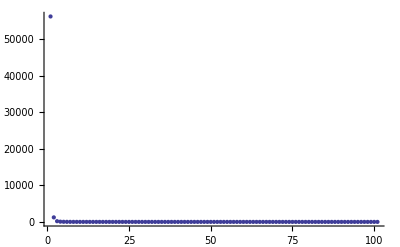

```mathematica
ListPlot[WW]
```

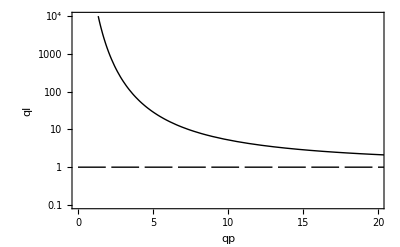

```mathematica
a1=LogPlot[{RR00[x] ,1},{x,0,40},Frame->True,PlotRange->{{0,20},{0.1,10^4}},PlotStyle->{Black,{Black,Dashing[{0.05,0.01}]},{Black,Dashing[{0.005,0.001}]}},RotateLabel->False,FrameLabel->{"qp","ql"}]
```

```mathematica
a1=LogPlot[{RR02[x] ,1},{x,0,40},Frame->True,PlotRange->{{0,40},{0.1,10^4}},PlotStyle->{Black,{Black,Dashing[{0.05,0.01}]},{Black,Dashing[{0.005,0.001}]}},RotateLabel->False,FrameLabel->{"qp","ql"}]
```

```mathematica
Export["fig2.eps",a1,"eps"];
```

```mathematica
Qnres[b_,y_,t_]:=(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] b((2 Subscript[α, e] b)/π )^(15/4) (((2*28*y)/(3*56*b))^2*1.009^6+1)^-3(t)^(3/2) Exp[-((2 Subscript[α, e] b)/(π (t)^2))^(1/2)] RR00[1/2((2 Subscript[α, e] b)/(π (t)^2))^(1/2)]
```

```mathematica
Qnres[1000,0.17]
```

5.2374×10^9

```mathematica
Q0res[b_,mu_,t_]:=((2 b)^(9/2)Subscript[Gm, e]^2)/(12 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[((x1+x2)(x1 x2-1+Exp[-x1 x2]))/((1+Exp[(√(2 b))/(2 t)(x1+x1^-1)-mu/t])(1+Exp[(√(2 b))/(2 t)(x2-x1^-1)+mu/t])),{x1,0,∞},{x2,0,x1^-1}]
```

```mathematica
Q0res[50,6.92,0.17]
```

3.15603×10^12

```mathematica
Qres[b_,y_,t_]:=(Subscript[Gm, e]^2*Subscript[Q, e]*(1-9 Exp[-1]/4))/(9*2^(1/4)*π^(9/2))*(Subscript[g, V]^2+Subscript[g, A]^2)(b)^(17/4) √t Exp[(√(((2*28*y)/(3*56*b))^2*1.009^6+1))/t-(√(2 b))/t]
```

```mathematica
Qres[50,1000,0.17]
```

1.49125×10^18

```mathematica
√(((2*28*1000)/(3*56*50))^2*1.009^6+1)
```

6.92092

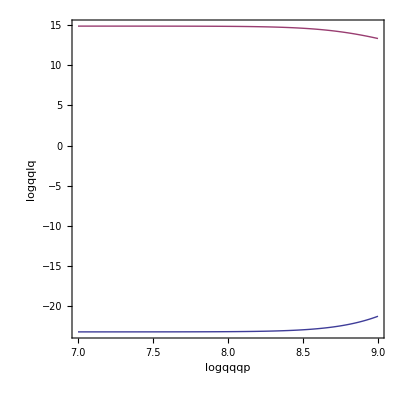

```mathematica
ParametricPlot[{{Log[10,10^6*y],Log[10,Q0res[227,√(((2*28*y)/(3*56*227))^2*1.009^6+1),0.17]]},{Log[10,10^6*y],Log[10,Qnres[227,y,0.17]]}},{y,10,1000},Frame->True,AspectRatio->1/1,RotateLabel->False,FrameLabel->{"logqqqp","logqqlq"}]
```

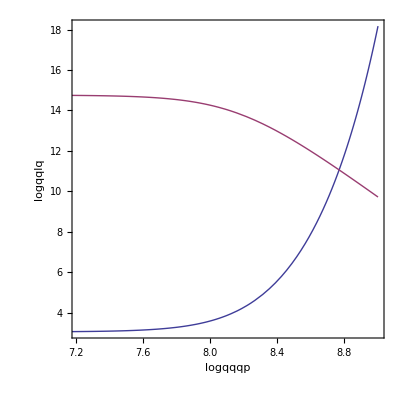

```mathematica
ParametricPlot[{{Log[10,10^6*y],Log[10,Qres[y,0.17]]},{Log[10,10^6*y],Log[10,Qnres[y,0.17]]}},{y,1,1000},Frame->True,AspectRatio->1/1,RotateLabel->False,FrameLabel->{"logqqqp","logqqlq"}]
```

```mathematica
,PlotRange->{{6,9},{1,2}}
```

## Resonant scattering

```mathematica
Fres1[γ_,η_]:=NIntegrate[(u^3 (1+x) (γ u (1+x) +1-γ u^2 (1-x^2)/2)^2)/(1-Exp[-(1/(u (1-x))-(γ u (1+x))/2-γ) *η/γ])*((1/(u (1-x))-(γ u (1+x))/2-γ)*(1-Exp[-(γ u)/2 (1-x^2)]))/(Exp[η/γ (1/(u (1-x))-(γ u (1-x))/2-γ)]-1),{u,0,∞},{x,-1,1}];
```

```mathematica
Fres1[10^4,10^5]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2.44942×10^-90

Neutrino synchrotron radiation

```mathematica
Integrate[(ql^2-x) Exp[-x/β],{x,0,ql^2}]
```

β (ql^2+(-1+ⅇ^(-ql^2/β)) β)

```mathematica
μ1=√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)
```

150.847

```mathematica
SynhYaKam[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[((x+β/μ1^2)^2(1-x) (x-1+Exp[-x]))/(Exp[μ1/t(x+β/μ1^2)]-1),{x,0,1}];
```

```mathematica
SynhYaKam[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

31492.

```mathematica
SynhYaKam0[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[(x^2(1-x) (x-1+Exp[-x]))/(Exp[μ1/t x]-1),{x,0,1}];
```

```mathematica
SynhYaKam0[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

47634.1

```mathematica
Synh[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[(x^2(1-x) (x-1+Exp[-x]))/(Exp[μ1/t x]-1),{x,0,1}];
```

```mathematica
Synh[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

47634.1

```mathematica
Synh1[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[x^2(1-x) (x-1+Exp[-x])Exp[-μ1/t x],{x,0,1}];
```

```mathematica
Synh1[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

45936.9

```mathematica
Synh0[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (2  t β^2)/μ1^5 Exp[-(√(2 β))/t];
```

```mathematica
Synh0[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

1.33096×10^-35

```mathematica
Synh00[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (12  t^5)/μ1^5;
```

```mathematica
Synh00[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

45977.6

```mathematica
(2*28)/(3*56)//N
```

0.333333

```mathematica
a1=Integrate[x^2(1-x) (x-1+Exp[-x])Exp[-a x],{x,0,1}]
```

(ⅇ^(-a-1) (a^7+2 (3+ⅇ) a^6+(11+20 ⅇ) a^5+12 ⅇ (7+ⅇ^a) a^4-16 ⅇ (-11+2 ⅇ^a) a^3-2 ⅇ (-97+49 ⅇ^a) a^2-12 ⅇ (-9+7 ⅇ^a) a-24 ⅇ (-1+ⅇ^a)))/(a^5 (a+1)^4)

```mathematica
Series[a1,{a,∞,5}]
```

ⅇ^(-a-1) (((1/a)^2+O((1/a)^3))+ⅇ^a (12 ⅇ (1/a)^5+O((1/a)^6)))

```mathematica
a1/.{a->μ1/0.02,b->(√(2*2.27))/μ1}
```

1.4502×10^-58

γ=(√(2eB))/(2T)=(√β)/(√2 t)

β=B/B_e   x=ω/m   t=T/m    μ1 = μ/m

```mathematica
22.7*4.41
```

100.107

```mathematica
√(2*22.7)
```

6.73795

```mathematica
ωp[β_]:=√((2 Subscript[α, e] β)/π);
```

```mathematica
ωp[22.7]
```

0.32474

```mathematica
200/μ1[200,2.3*10^3,1]
```

9.79985

```mathematica
μ1[β_,ρ6_,n_]:=√(((2*28*ρ6)/(3*56*β))^2*1.009^6+2 β n+1);
```

```mathematica
μ1[22.7,10^3,0]
```

15.1175

```mathematica
F1[β_,x_,t_,ρ6_,n_]:=(1+Exp[(2β-x^2)/(2 x t)-μ1[β,ρ6,n]/t])^-1(1+Exp[-(2β+x^2)/(2 x t)+μ1[β,ρ6,n]/t] )^-1 ;
```

```mathematica
Plot[F1[22.7,x,0.17,10^2,1],{x,2,6},PlotRange->All]
```

```mathematica
F2[x_,t_,z_]:=(1-Exp[-z x/t])^-1 (1-Exp[-(1-z) x/t])^-1;
```

```mathematica
We0γen[β_,x_,t_,ρ6_,n_]:=(Subscript[α, e] β)/x (2-(2 Subscript[α, e] β)/(x^2 π)) (1+Exp[(2β-x^2)/(2 x t)-μ1[β,ρ6,n]/t])^-1(1+Exp[-(2β+x^2)/(2 x t)+μ1[β,ρ6,n]/t] )^-1 ;
```

```mathematica
Wn0[β_,x_,t_,ρ6_,n_]:=(Subscript[α, e]^2 β)/π x/μ1[β,ρ6,n]^6 NIntegrate[z (1-2z)(1-Exp[-z x/t])^-1 (1-Exp[-(1-z) x/t])^-1,{z,-∞,1/2-(Subscript[α, e] β)/(x^2 π)}];
```

```mathematica
Wn011[β_,x_,t_]:=(Subscript[α, e]^2 x^3)/(2 π β)  NIntegrate[z (1-Exp[-z x/t])^-1 (1-Exp[-(1-z) x/t])^-1,{z,-∞,1/2}];
```

```mathematica
Wn021[β_,x_,t_]:=(Subscript[α, e]^2 x)/(2 π β)  (x^2-(2 Subscript[α, e] β)/π) NIntegrate[z (1-Exp[-z x/t])^-1 (1-Exp[-(1-z) x/t])^-1,{z,-∞,1/2}];
```

```mathematica
Wn012[β_,x_,t_,ρ6_,n_]:=(Subscript[α, e]^2 x^3)/(2 π β)   NIntegrate[z (1+z/μ1[β,ρ6,n]^2)^2  (1-Exp[-z x/t])^-1 (1-Exp[-(1-z) x/t])^-1,{z,-∞,1/2}];
```

```mathematica
We0γen[22.7,0.5,0.17,10^3,1]
```

4.5437×10^-74

```mathematica
Wn012[22.7,0.5,0.17,10^3,0]
```

2.21052×10^-8

```mathematica
Wn0[22.7,0.5,0.17,10^3,0]
```

7.67432×10^-12

```mathematica
Wn011[22.7,0.5,0.17]
```

2.21115×10^-8

```mathematica
Wn021[22.7,0.5,0.17]
```

1.27844×10^-8

```mathematica
We0γen[200,2,0.1,2.3*10^3,1]
```

6.19354432757271×10^-342

```mathematica
LogPlot[{We0γen[200,x,0.1,2.3*10^3,1],Wn0[200,x,0.1,2.3*10^3,0]},{x,0.4,10},PlotRange->{{0.5,10},{10^-12,10}},Frame->True,FrameLabel->{k1,k2},RotateLabel->False]
```

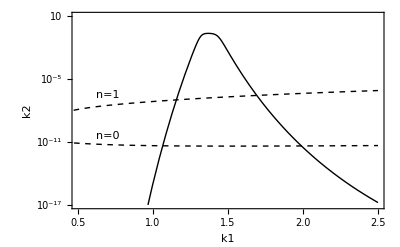

```mathematica
a1=Show[LogPlot[{We0γen[22.7,x,0.17,10^3,1],Wn0[22.7,x,0.17,10^3,0],Wn021[22.7,x,0.17]},{x,0.4,2.5},PlotRange->{{0.5,2.5},{10^-17,10}},Frame->True,FrameLabel->{k1,k2},RotateLabel->False,PlotStyle->{Black,{Black,Dashing[{0.01,0.01}]},{Black,Dashing[{0.01,0.01}]}}],Graphics[{Text["n=0",{0.7,-24}]}],Graphics[{Text["n=1",{0.7,-15}]}]]
```

```mathematica
Export["rr.eps",a1,"eps"];
```

```mathematica
Plot[Wn0[22.7,x,0.17,10^3,0],{x,0.4,2},PlotRange->All,Frame->True]
```

```mathematica
RR[β_,x_,t_,ρ6_,n_]:=Subscript[α, e]/π x^2/μ1[β,ρ6,n]^6 (1+Exp[(2β-x^2)/(2 x t)-μ1[β,ρ6,n]/t]) (1+Exp[-(2β+x^2)/(2 x t)+μ1[β,ρ6,n]/t] ) (2-(2 Subscript[α, e] β)/(x^2 π))^-1 NIntegrate[z (1-2z)(1-Exp[-z x/t])^-1 (1-Exp[-(1-z) x/t])^-1,{z,-∞,1/2-(Subscript[α, e] β)/(x^2 π)}];
```

```mathematica
RR[22.7,2.38,0.17,10^2,1]
```

0.0000107034

```mathematica
Qs0[β_,η_,t_]:=(8 Subscript[Gm, e]^2 √(2 β) β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[x(x^2-z^2-1+Exp[-(x^2-z^2)])*(Φ1[x,z,η,β,t]+Φ1[x,-z,η,β,t]),{x,1,∞},{z,√(x^2-1),x}];
```

```mathematica
Qs0[100,1,2]
```

9.64281×10^23